## Load data

```mathematica
SetDirectory@NotebookDirectory[];
data=Import["../_Data/supplementary_data.xlsx"];
docs=data[[3]]; (*COLUMN NAMES: {"id","original","place","Latitude","Longitude","year","month","other","vydavatel","vydavatel2"}*)
docs[[2;;All,5]]=Round@docs[[2;;All,5]]; (*round years*)
docList=docs[[2;;All,1]]; (* document names only *)
issuerList=Union[docs[[2;;All,-2]]];  (* issuer names only *)
yearList=Union[docs[[2;;All,5]]];
missing={#,0}&/@Complement[Range[yearList[[1]],yearList[[-1]]],yearList];
(* years without any documents *)
funcList=data[[6,2;;All]]; (* function names only *)

incid=data[[4]]/.""->0;
names=DeleteCases[Drop[incid[[All,2]],1],0];
incid=incid[[2;;Length@names+1,Flatten[Position[incid[[1]],#]&/@docList]]];(* Same ordering as in docs *)
incidFunc=incid;
incid=incid/._String->1;
incid=SparseArray[incid,{Length@names,Length@docList}];

funcDS=Import["_Data/funcDS.m"];
```

### Functions

```mathematica
makeNet[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]].Transpose[incid[[All,selectPos]]]-SparseArray@IdentityMatrix[Length[names]],Automatic,0]; (* make adjacency from incidence matrix *)
adjNam=DeleteCases[adjNam,PatternSequence[{x_,x_}->_]];
AppendTo[adjNam,{_,_}->∞];
g=WeightedAdjacencyGraph[SparseArray[adjNam,Length[names]]];
{adjNam,g}
];
```

```mathematica
makeFunc[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
incidFunc[[All,selectPos]]
];
```

```mathematica
Clear[calcRank];
(* alpha parameter used following: Opsahl et al. 2010 *)
calcRank[net_,type_,alpha_]:=calcRank[net,type,alpha]=Module[{d,s,vv,sg,ng,temp,maxRank,centrality,comps},
comps=ConnectedComponents[net[[2]]];
sg=Subgraph[net[[2]],comps[[1]]];
centrality=ConstantArray[0,VertexCount@net[[2]]];

Switch[type,
"d",d=VertexDegree[sg];s=Total@WeightedAdjacencyMatrix[sg];centrality[[VertexList[sg]]]=Switch[alpha,0,d,1,s,_,(If[#==0,0,#^(1-alpha)]&/@d)s^alpha];,
"e",{vv}=Eigenvectors[1.Normal@If[alpha==0,AdjacencyMatrix[sg],WeightedAdjacencyMatrix[sg]],1];
centrality[[VertexList[sg]]]=Normalize[Abs[vv],Total];,
"b"(* no weighted paths in this version *),ng=Graph[VertexList[net[[2]]],{Null,AdjacencyMatrix[net[[2]]]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[net[[2]],EdgeWeight]^-alpha];centrality=BetweennessCentrality[ng];,
"c",ng=Graph[VertexList[sg],{Null,AdjacencyMatrix[sg]}];
ng=SetProperty[ng,EdgeWeight->PropertyValue[sg,EdgeWeight]^-alpha];
centrality[[VertexList[sg]]]=ClosenessCentrality[ng];
];

temp=MapIndexed[({#1/.{x_,_?NumberQ}:>x,#2[[1]]-1})&,GatherBy[SortBy[Transpose[{Range[Length[names]],centrality}],Last],Last]];
maxRank=Max@Transpose[temp][[2]];
temp=Sort@Flatten[Transpose@{#[[1]],ConstantArray[#[[2]]/maxRank,Length[#[[1]]]]}&/@temp,1]
];
cent2rank[centrality_]:=Module[{temp,maxRank},
temp=MapIndexed[({#1/.{x_,_?NumberQ}:>x,#2[[1]]-1})&,GatherBy[SortBy[Transpose[{Range[Length[names]],centrality}],Last],Last]];
maxRank=Max@Transpose[temp][[2]];
temp=Sort@Flatten[Transpose@{#[[1]],ConstantArray[#[[2]]/maxRank,Length[#[[1]]]]}&/@temp,1];
temp[[All,2]]
];
```

### Make networks

```mathematica
wholeNet=makeNet[yearList[[1]],yearList[[-1]]];
nn=VertexCount[wholeNet[[2]]];
ee=EdgeCount[wholeNet[[2]]];
```

```mathematica
segments={1243,1248,1250,1252,1254,1257};
nets=Table[
makeNet[segments[[c]],segments[[c+1]]-1]
,{c,1,Length@segments-1}];
```

## Individual noblemen ranked based on their centrality

### Individuals with highest centrality

```mathematica
temp=Normal@funcDS[All,1,All,"c1.5"];
names[[Join[{1979},Ordering[Mean@temp,-5]]]]
```

{Václav I.,Pardus,Boček z Jaroslavic,Jan z Deblína, syn Ratibora,Vítek z Hradce, syn Jindřicha,Přemysl II.}

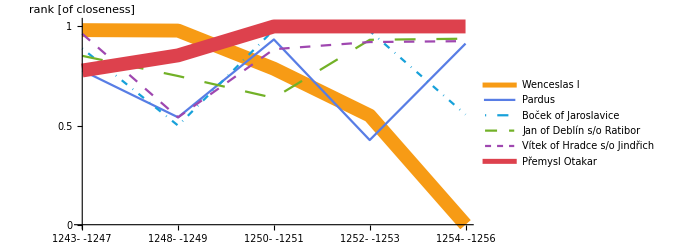

```mathematica
colorsKing={Directive[(*Blue*)RGBColor[0.97, 0.606, 0.081],(*Dashing[0.015],*)Thickness[0.02]],Directive[(*Green*)RGBColor[0.34398, 0.49112, 0.89936],Thick],Directive[(*Black*)RGBColor[0.09096, 0.6296, 0.85532],Thick,DotDashed],Directive[(*Blue*)RGBColor[0.448, 0.69232, 0.1538],Dashing[0.03],Thick],Directive[(*Red*)RGBColor[0.62168, 0.2798, 0.6914],Thick,Dashing[0.015]],Directive[(*Red*)RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],Thickness[0.02]]};

ListLinePlot[
Transpose@temp[[All,Join[{1979},Ordering[Mean@temp,-5]]]],
PlotRange->{{1,5},{0,1.02}},PlotStyle->colorsKing,PlotLegends->{"Wenceslas I","Pardus","Boček of Jaroslavice","Jan of Deblín s/o Ratibor","Vítek of Hradce s/o Jindřich","Přemysl Otakar"},AxesLabel->{None,"rank\n[of closeness]"},LabelStyle->{FontFamily->"Helveticae",FontSize->18,Black},FrameStyle->Automatic,Ticks->{Table[
{c,If[c==2,Style[ToString@cezury[[c]]<>"-\n-"<>ToString[cezury[[c+1]]-1],Red,Bold],ToString@cezury[[c]]<>"-\n-"<>ToString[cezury[[c+1]]-1]]}
,{c,1,Length@cezury-1}],{0,.5,1}},FrameTicksStyle->Directive[FontSize->14,FontFamily->"Helveticae",Black],GridLines->None(*{{0},{0}}*),ImageSize->500,AspectRatio->1/2]
```

### Documents issued during war

```mathematica
wardocs=Flatten[Position[docList,#]&/@{"T2_164","T2_165","T2_167","T2_169"}];
Grid@SortBy[{names[[#[[1]]]],#[[1]],docList[[wardocs[[#[[2]]]]]]}&/@ArrayRules[incid[[All,wardocs]]][[All;;-2,1]],#[[3]]&]
```

Častolov, syn Smila, bratr Jindřicha | 330 | T2_164
Havel z Lemberka | 599 | T2_164
Jindřich, syn Častolova | 900 | T2_164
Ojíř z Frídberka | 1277 | T2_164
Siffrido de Colbowe | 1791 | T2_164
Častolov, syn Smila, bratr Jindřicha | 330 | T2_165
Havel z Lemberka | 599 | T2_165
Jindřich, syn Častolova | 900 | T2_165
Ojíř z Frídberka | 1277 | T2_165
Siffrido de Colbowe | 1791 | T2_165
Václav I. | 1979 | T2_165
Beneš, syn Heřmana, bratr Markvarta | 112 | T2_167
Častolov, syn Smila, bratr Jindřicha | 330 | T2_167
Havel z Lemberka | 599 | T2_167
Jaroslav z Hruštice, syn Markvarta | 811 | T2_167
Václav I. | 1979 | T2_167
Boreš, syn Bohuslava z Rýzmberka | 238 | T2_169
Častolov, syn Smila, bratr Jindřicha | 330 | T2_169
Havel z Lemberka | 599 | T2_169
Jan Losos | 752 | T2_169
Jaroš ze Slivna | 806 | T2_169
Jindřich Král | 859 | T2_169
Jindřich, syn Častolova | 900 | T2_169
Lutholdus | 1056 | T2_169
Smil z Lichtenburka | 1832 | T2_169
Václav I. | 1979 | T2_169

### Noblemen loyal to Wenceslas (from historiography)

```mathematica
(* podzieleni rodzinami *)
```

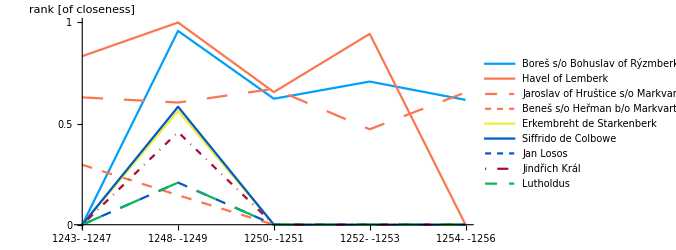
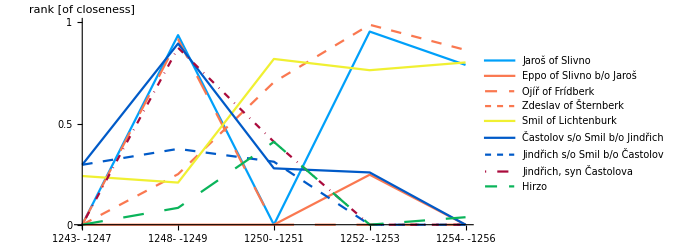
-Graphics- | -Graphics-

```mathematica
colors={(*Directive[Black,Thick],*)Directive[RGBColor[0., 0.6274509803921569, 0.9803921568627451],Thick],Directive[RGBColor[0.9803921568627451, 0.47058823529411764, 0.3137254901960784],Thick],Directive[RGBColor[0.9803921568627451, 0.47058823529411764, 0.3137254901960784],Thick,Dashing[0.03]],Directive[RGBColor[0.9803921568627451, 0.47058823529411764, 0.3137254901960784],Thick,Dashing[0.015]],Directive[RGBColor[0.9411764705882353, 0.9411764705882353, 0.19607843137254902],Thick],Directive[RGBColor[0., 0.35294117647058826, 0.7843137254901961],Thick],Directive[RGBColor[0., 0.35294117647058826, 0.7843137254901961],Thick,Dashing[0.015]],Directive[RGBColor[0.6666666666666666, 0.0392156862745098, 0.23529411764705882],Thick,DotDashed],Directive[RGBColor[0.0392156862745098, 0.7058823529411765, 0.35294117647058826],Thick,Dashing[0.03]],Directive[RGBColor[0.9803921568627451, 0.47058823529411764, 0.9803921568627451],Thick,Dashing[0.03]],Directive[RGBColor[0.6274509803921569, 0.9803921568627451, 0.5098039215686274],Thick],Directive[RGBColor[0.6274509803921569, 0.9803921568627451, 0.5098039215686274],Thick,Dashing[0.03]],Directive[RGBColor[0.6274509803921569, 0.9803921568627451, 0.5098039215686274],Thick,Dashing[0.015]],Directive[RGBColor[0.0784313725490196, 0.8235294117647058, 0.8627450980392157],Thick,DotDashed],Directive[RGBColor[0.5098039215686274, 0.0784313725490196, 0.6274509803921569],Dashing[0.03],Thick],Directive[RGBColor[0., 0.43137254901960786, 0.5098039215686274],Thick],Directive[RGBColor[0.9803921568627451, 0.9019607843137255, 0.7450980392156863],Thick]};

{{temp=MapIndexed[Tooltip[Normal@funcDS[All,1,#1, "c1.5"],#2[[1]]]&,Flatten@{{(*1979,1553,*) 238},{599,811,112},{518,1791,752,859,1056}}];
ListLinePlot[
temp,PlotRange->{{1,5},{0,1.}},PlotStyle->colors,PlotLegends->{(*"Václav I.","Přemysl II.",*)"Boreš s/o Bohuslav of Rýzmberk","Havel of Lemberk","Jaroslav of Hruštice s/o Markvart","Beneš s/o Heřman b/o Markvart","Erkembreht de Starkenberk","Siffrido de Colbowe","Jan Losos","Jindřich Král","Lutholdus","Jaroš of Slivno","Eppo of Slivno b/o Jaroš","Ojíř of Frídberk","Zdeslav of Šternberk","Hirzo","Častolov s/o Smil b/o Jindřich","Jindřich s/o Smil b/o Častolov","Jindřich, syn Častolova","Smil of Lichtenburk"},AxesLabel->{None,"rank\n[of closeness]"},LabelStyle->{FontFamily->"Helveticae",FontSize->18,Black},FrameStyle->Automatic,Ticks->{Table[
{c,If[c==2,Style[ToString@cezury[[c]]<>"-\n-"<>ToString[cezury[[c+1]]-1],Red,Bold],ToString@cezury[[c]]<>"-\n-"<>ToString[cezury[[c+1]]-1]]}
,{c,1,Length@cezury-1}],{0,.5,1}},FrameTicksStyle->Directive[FontSize->14,FontFamily->"Helveticae",Black],GridLines->None(*{{0},{0}}*),ImageSize->500,AspectRatio->1/2],
temp=MapIndexed[Tooltip[Normal@funcDS[All,1,#1,18 (*c1.5*)],#2[[1]]]&,Flatten@{{806,514},{1277,2302},{1832,330,906,900,642}}];
ListLinePlot[
temp,PlotRange->{{1,5},{0,1.}},PlotStyle->colors,PlotLegends->{"Jaroš of Slivno","Eppo of Slivno b/o Jaroš","Ojíř of Frídberk","Zdeslav of Šternberk","Smil of Lichtenburk","Častolov s/o Smil b/o Jindřich","Jindřich s/o Smil b/o Častolov","Jindřich, syn Častolova","Hirzo"},AxesLabel->{None,"rank\n[of closeness]"},LabelStyle->{FontFamily->"Helveticae",FontSize->18,Black},FrameStyle->Automatic,Ticks->{Table[
{c,If[c==2,Style[ToString@cezury[[c]]<>"-\n-"<>ToString[cezury[[c+1]]-1],Red,Bold],ToString@cezury[[c]]<>"-\n-"<>ToString[cezury[[c+1]]-1]]}
,{c,1,Length@cezury-1}],{0,.5,1}},FrameTicksStyle->Directive[FontSize->14,FontFamily->"Helveticae",Black],GridLines->None,ImageSize->500,AspectRatio->1/2]}}//Grid
```

### Rebels (known from historiography)

```mathematica
names[[{2070,1392,1350,757,1817,2041,707,1183,1850,145,327,376}]]
```

{Vítek z Hradce, syn Jindřicha,Pardus,Oneš, syn Bicena z Pňovic,Jan z Deblína, syn Ratibora,Slavibor z Drnovic,Vilém z Náměšti, syn Slavibora,Idík, syn Milíče,Milíč z Náměšti,Spitata z Moravičan,Boček z Jaroslavic,Častolov z Čeblovic, bratr Crha,Crh, bratr Častolova}

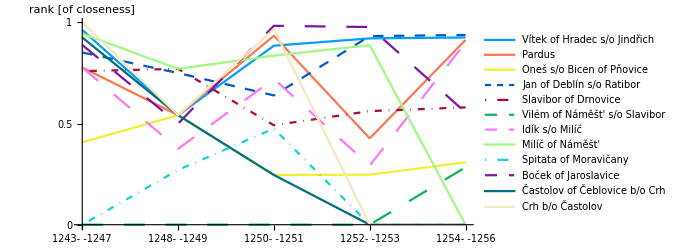

```mathematica
colors={Directive[RGBColor[0., 0.6274509803921569, 0.9803921568627451],Thick],Directive[RGBColor[0.9803921568627451, 0.47058823529411764, 0.3137254901960784],Thick],Directive[RGBColor[0.9411764705882353, 0.9411764705882353, 0.19607843137254902],Thick],Directive[RGBColor[0., 0.35294117647058826, 0.7843137254901961],Thick,Dashing[0.015]],Directive[RGBColor[0.6666666666666666, 0.0392156862745098, 0.23529411764705882],Thick,DotDashed],Directive[RGBColor[0.0392156862745098, 0.7058823529411765, 0.35294117647058826],Thick,Dashing[0.03]],Directive[RGBColor[0.9803921568627451, 0.47058823529411764, 0.9803921568627451],Thick,Dashing[0.03]],Directive[RGBColor[0.6274509803921569, 0.9803921568627451, 0.5098039215686274],Thick],Directive[RGBColor[0.0784313725490196, 0.8235294117647058, 0.8627450980392157],Thick,DotDashed],Directive[RGBColor[0.5098039215686274, 0.0784313725490196, 0.6274509803921569],Dashing[0.03],Thick],Directive[RGBColor[0., 0.43137254901960786, 0.5098039215686274],Thick],Directive[RGBColor[0.9803921568627451, 0.9019607843137255, 0.7450980392156863],Thick]};

temp=MapIndexed[Tooltip[Normal@funcDS[All,1,#1,"c1.5"],#2[[1]]]&,{2070,1392,1350,757,1817,2041,707,1183,1850,145,327,376}];
ListLinePlot[
temp,PlotRange->{{1,5},{0,1.}},PlotStyle->colors,PlotLegends->{"Vítek of Hradec s/o Jindřich","Pardus","Oneš s/o Bicen of Pňovice","Jan of Deblín s/o Ratibor","Slavibor of Drnovice","Vilém of Náměšt' s/o Slavibor","Idík s/o Milíč","Milíč of Náměšt'","Spitata of Moravičany","Boček of Jaroslavice","Častolov of Čeblovice b/o Crh","Crh b/o Častolov"},AxesLabel->{None,"rank\n[of closeness]"},LabelStyle->{FontFamily->"Helveticae",FontSize->18,Black},FrameStyle->Automatic,Ticks->{Table[
{c,If[c==2,Style[ToString@cezury[[c]]<>"-\n-"<>ToString[cezury[[c+1]]-1],Red,Bold],ToString@cezury[[c]]<>"-\n-"<>ToString[cezury[[c+1]]-1]]}
,{c,1,Length@cezury-1}],{0,.5,1}},FrameTicksStyle->Directive[FontSize->14,FontFamily->"Helveticae",Black],GridLines->None,ImageSize->500,AspectRatio->1/2]
```